```mathematica
ClearAll["Global`*"]
h=1;
ϕ=1;
eqn1=D[u[y,θ,z],y]+D[v[y,θ,z],θ]+D[v[y,θ,z],θ]==0;
eqn2=D[p[y,θ,z],y]==0;
eqn3=-D[p[y,θ,z],θ]+D[v[y,θ,z],{y,2}]-Cos[θ]/ϕ==0;
eqn4=-D[p[y,θ,z],z]+D[w[y,θ,z],{y,2}]==0;
sol=NDSolve[
{eqn1,eqn2,eqn3,eqn4,
(*boundary conditions*)
p[y,θ,z]==-1/(ϕ Bo),D[v[h,θ,z],y]==0,D[w[h,θ,z],y]==0,u[0,θ,z]==0, v[0,θ,z]==0,w[0,θ,z]==0},{u,v,w,p},{y,θ,z}]
```

NDSolve[{2 v^(0,1,0)[y,θ,z]+u^(1,0,0)[y,θ,z]==0,p^(1,0,0)[y,θ,z]==0,-Cos[θ]-p^(0,1,0)[y,θ,z]+v^(2,0,0)[y,θ,z]==0,-p^(0,0,1)[y,θ,z]+w^(2,0,0)[y,θ,z]==0,p[y,θ,z]==-1/Bo,True,True,u[0,θ,z]==0,v[0,θ,z]==0,w[0,θ,z]==0},{u,v,w,p},{y,θ,z}]

```mathematica
ClearAll["Global`*"]
M=1;
W=0.001;
Bo=1;
eqn= -M W D[h[x],x]+D[(h[x]^3/3)Cos[x],x]-D[(h[x]^3/(3 Bo))D[h[x]+D[h[x],{x,2}]]+(h[x]^3/3)(W^2-Sin[x])D[h[x],x]]==0;
sol=NDSolve[{eqn,h[0]==0.01,h[2π]==0.01},h,{x,0,2π}]
```

{{h→InterpolatingFunction[…]}}

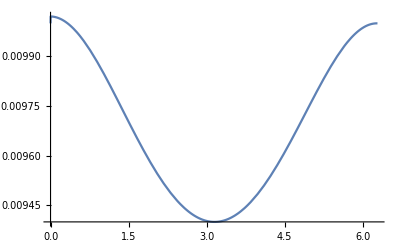

```mathematica
Plot[h[x]/.sol,{x,0,2π}]
```